Answer 1(a)
Let 1/(4 πϵ_0)=1

```mathematica
V=q1/(√((x-a)^2+(y-a)^2))+q2/(√((x+a)^2+(y-a)^2))+q3/(√((x+a)^2+(y+a)^2))+q4/(√((x-a)^2+(y+a)^2));
Elec=-Grad[V,{x,y}]
```

{(q1 (-a+x))/(((-a+x)^2+(-a+y)^2)^(3/2))+(q2 (a+x))/(((a+x)^2+(-a+y)^2)^(3/2))+(q4 (-a+x))/(((-a+x)^2+(a+y)^2)^(3/2))+(q3 (a+x))/(((a+x)^2+(a+y)^2)^(3/2)),(q1 (-a+y))/(((-a+x)^2+(-a+y)^2)^(3/2))+(q2 (-a+y))/(((a+x)^2+(-a+y)^2)^(3/2))+(q4 (a+y))/(((-a+x)^2+(a+y)^2)^(3/2))+(q3 (a+y))/(((a+x)^2+(a+y)^2)^(3/2))}

```mathematica
Manipulate[VectorPlot[{(q1 (-a+x))/(((-a+x)^2+(-a+y)^2)^(3/2))+(q2 (a+x))/(((a+x)^2+(-a+y)^2)^(3/2))+(q4 (-a+x))/(((-a+x)^2+(a+y)^2)^(3/2))+(q3 (a+x))/(((a+x)^2+(a+y)^2)^(3/2)),(q1 (-a+y))/(((-a+x)^2+(-a+y)^2)^(3/2))+(q2 (-a+y))/(((a+x)^2+(-a+y)^2)^(3/2))+(q4 (a+y))/(((-a+x)^2+(a+y)^2)^(3/2))+(q3 (a+y))/(((a+x)^2+(a+y)^2)^(3/2))},{x,-10,10},{y,-10,10}],{{a,1},-10,10},{{q1,1},-5,5},{{q2,1},-5,5},{{q3,1},-5,5},{{q4,1},-5,5}]
```

Aliter 1(a)

```mathematica
Manipulate[Show[VectorPlot[{EX[x,y,Q1[[1]],Q1[[2]],q1]+EX[x,y,Q2[[1]],Q2[[2]],q2]+EX[x,y,Q3[[1]],Q3[[2]],q3]+EX[x,y,Q4[[1]],Q4[[2]],q4],EY[x,y,Q1[[1]],Q1[[2]],q1]+EY[x,y,Q2[[1]],Q2[[2]],q2]+EY[x,y,Q3[[1]],Q3[[2]],q3]+EY[x,y,Q4[[1]],Q4[[2]],q4]},{x,-20,20},{y,-15,15},VectorScale->{Automatic,Automatic,None}(*determines the length and arrowhead size of field vectors that are drawn.*),VectorColorFunction->"Rainbow",AspectRatio->.75],Graphics[{RGBColor[{Boole[q1<0],0,0}],Circle[{Q1[[1]],Q1[[2]]},1.25],Text[Style[N[q1],10,Bold],{Q1[[1]],Q1[[2]]}],RGBColor[{Boole[q2<0],0,0}],Circle[{Q2[[1]],Q2[[2]]},1.25],Text[Style[N[q2],10,Bold],{Q2[[1]],Q2[[2]]}],RGBColor[{Boole[q3<0],0,0}],Circle[{Q3[[1]],Q3[[2]]},1.25],Text[Style[N[q3],10,Bold],{Q3[[1]],Q3[[2]]}],RGBColor[{Boole[q4<0],0,0}],Circle[{Q4[[1]],Q4[[2]]},1.25],Text[Style[N[q4],10,Bold],{Q4[[1]],Q4[[2]]}]}],ImageSize->{575,375}],(*Charge values controlled by sliders*){{q1,1},-2,2,.1},{{q2,-1},-2,2,.1},{{q3,1},-2,2,.1},{{q4,-1},-2,2,.1},(*Charge positions (fixed for quadrupole)*){{Q1,{-10,10}}},{{Q2,{10,10}}},{{Q3,{-10,-10}}},{{Q4,{10,-10}}},(*Electric field components*)Initialization:>(EX[x_,y_,xq_,yq_,qn_]:=((x-xq) qn)/((x-xq)^2+(y-yq)^2)^(3/2);
EY[x_,y_,xq_,yq_,qn_]:=((y-yq) qn)/((x-xq)^2+(y-yq)^2)^(3/2))]
```

```mathematica
Elec1[x_,y_]:=-Grad[V,{x,y}]
Manipulate[VectorPlot[Elec1[x_,y_],{x,-10,10},{y,-10,10}],{{a,1},-5,5},{{q1,1},-5,5},{{q2,1},-5,5},{{q3,1},-5,5},{{q4,1},-5,5}]
```

```mathematica
Manipulate[VectorPlot[{(q(-a+x))/(((-a+x)^2+(-a+y)^2)^(3/2))+(-q (a+x))/(((a+x)^2+(-a+y)^2)^(3/2))+(-q(-a+x))/(((-a+x)^2+(a+y)^2)^(3/2))+(q(a+x))/(((a+x)^2+(a+y)^2)^(3/2)),(q(-a+y))/(((-a+x)^2+(-a+y)^2)^(3/2))+(-q (-a+y))/(((a+x)^2+(-a+y)^2)^(3/2))+(-q(a+y))/(((-a+x)^2+(a+y)^2)^(3/2))+(q(a+y))/(((a+x)^2+(a+y)^2)^(3/2))},{x,-10,10},{y,-10,10}],{{a,1},-5,5},{{q,1},-5,5}]
```

## Answer 1(b)

```mathematica
Manipulate[
Show[
StreamPlot[{EX[x,y,Q1[[1]],Q1[[2]],q1]+EX[x,y,Q2[[1]],Q2[[2]],q2]+EX[x,y,Q3[[1]],Q3[[2]],q3]+EX[x,y,Q4[[1]],Q4[[2]],q4],EY[x,y,Q1[[1]],Q1[[2]],q1]+EY[x,y,Q2[[1]],Q2[[2]],q2]+EY[x,y,Q3[[1]],Q3[[2]],q3]+EY[x,y,Q4[[1]],Q4[[2]],q4]},{x,-20,20},{y,-15,15},VectorColorFunction->"Rainbow"],
Graphics[{RGBColor[{Boole[q1<0],0,0}],Circle[{Q1[[1]],Q1[[2]]},1.25],Text[Style[N[q1],10,Bold],{Q1[[1]],Q1[[2]]}],RGBColor[{Boole[q2<0],0,0}],Circle[{Q2[[1]],Q2[[2]]},1.25],Text[Style[N[q2],10,Bold],{Q2[[1]],Q2[[2]]}],RGBColor[{Boole[q3<0],0,0}],Circle[{Q3[[1]],Q3[[2]]},1.25],Text[Style[N[q3],10,Bold],{Q3[[1]],Q3[[2]]}],RGBColor[{Boole[q4<0],0,0}],Circle[{Q4[[1]],Q4[[2]]},1.25],Text[Style[N[q4],10,Bold],{Q4[[1]],Q4[[2]]}]}]],
(*Charge values sliders*){{q1,1},-2,2,.1},{{q2,-1},-2,2,.1},{{q3,1},-2,2,.1},{{q4,-1},-2,2,.1},
(*Charge positions(fixed for quadrupole)*){{Q1,{-10,10}}},{{Q2,{10,10}}},{{Q3,{-10,-10}}},{{Q4,{10,-10}}},
(*Electric field components*)Initialization:>(EX[x_,y_,xq_,yq_,qn_]:=((x-xq) qn)/((x-xq)^2+(y-yq)^2)^(3/2);
EY[x_,y_,xq_,yq_,qn_]:=((y-yq) qn)/((x-xq)^2+(y-yq)^2)^(3/2))]
```

Aliter 1(b)

```mathematica
Manipulate[StreamPlot[{(q(-a+x))/(((-a+x)^2+(-a+y)^2)^(3/2))+(-q (a+x))/(((a+x)^2+(-a+y)^2)^(3/2))+(-q(-a+x))/(((-a+x)^2+(a+y)^2)^(3/2))+(q(a+x))/(((a+x)^2+(a+y)^2)^(3/2)),(q(-a+y))/(((-a+x)^2+(-a+y)^2)^(3/2))+(-q (-a+y))/(((a+x)^2+(-a+y)^2)^(3/2))+(-q(a+y))/(((-a+x)^2+(a+y)^2)^(3/2))+(q(a+y))/(((a+x)^2+(a+y)^2)^(3/2))},{x,-10,10},{y,-10,10}],{{a,1},-5,5},{{q,1},-5,5}]
```

## Aliter 1(b)

```mathematica
Manipulate[Show[StreamPlot[{EX[x,y,Q1[[1]],Q1[[2]],q1]+EX[x,y,Q2[[1]],Q2[[2]],-q1],EY[x,y,Q1[[1]],Q1[[2]],q1]+EY[x,y,Q2[[1]],Q2[[2]],-q1]},{x,-15,15},{y,-15,15},AspectRatio->0.75,PlotRange->{{-15,15},{-15,15}}],(*Grounded Conducting Plane*)Graphics[{Thick,Black,Line[{{-15,0},{15,0}}]}],(*Charge and its Image*)Graphics[{RGBColor[{Boole[q1<0],0,0}],Circle[{Q1[[1]],Q1[[2]]},0.8],Text[Style[N[q1],12,Bold],{Q1[[1]],Q1[[2]]}],RGBColor[{Boole[-q1<0],0,0}],Circle[{Q2[[1]],Q2[[2]]},0.8],Text[Style[N[-q1],12,Bold],{Q2[[1]],Q2[[2]]}]}],ImageSize->{600,400}],(*Charge value slider*){{q1,1},-2,2,0.1},(*Position of real charge above plane*){{Q1,{0,5}},Locator},(*Image charge position (mirrored about plane)*)Initialization:>(Q2={Q1[[1]],-Q1[[2]]};
EX[x_,y_,xq_,yq_,qn_]:=((x-xq) qn)/((x-xq)^2+(y-yq)^2)^(3/2);
EY[x_,y_,xq_,yq_,qn_]:=((y-yq) qn)/((x-xq)^2+(y-yq)^2)^(3/2))]
```

Answer 1(c)

```mathematica
(*Manipulate[ContourPlot[{(q(-a+x))/(((-a+x)^2+(-a+y)^2)^(3/2))+(-q (a+x))/(((a+x)^2+(-a+y)^2)^(3/2))+(-q(-a+x))/(((-a+x)^2+(a+y)^2)^(3/2))+(q(a+x))/(((a+x)^2+(a+y)^2)^(3/2)),(q(-a+y))/(((-a+x)^2+(-a+y)^2)^(3/2))+(-q (-a+y))/(((a+x)^2+(-a+y)^2)^(3/2))+(-q(a+y))/(((-a+x)^2+(a+y)^2)^(3/2))+(q(a+y))/(((a+x)^2+(a+y)^2)^(3/2))},{x,-10,10},{y,-10,10}],{{a,1},-5,5},{{q,1},-5,5}]*)
```

```mathematica
Manipulate[ContourPlot[1/(√((x-a)^2+(y-a)^2))-1/(√((x+a)^2+(y-a)^2))+1/(√((x+a)^2+(y+a)^2))-1/(√((x-a)^2+(y+a)^2)),{x,-10,10},{y,-10,10},PlotLegends->Automatic],{{a,1},-5,5}]
```

## 1(c) Aliter

```mathematica
Manipulate[Show[ContourPlot[V[x,y,Q1[[1]],Q1[[2]],q1]+V[x,y,Q2[[1]],Q2[[2]],q2]+V[x,y,Q3[[1]],Q3[[2]],q3]+V[x,y,Q4[[1]],Q4[[2]],q4],{x,-20,20},{y,-15,15},Contours->20,PlotLegends->Automatic,ColorFunction->"BlueGreenYellow",ContourShading->True,AspectRatio->.75],Graphics[{RGBColor[{Boole[q1<0],0,0}],Circle[{Q1[[1]],Q1[[2]]},1.25],Text[Style[N[q1],10,Bold],{Q1[[1]],Q1[[2]]}],RGBColor[{Boole[q2<0],0,0}],Circle[{Q2[[1]],Q2[[2]]},1.25],Text[Style[N[q2],10,Bold],{Q2[[1]],Q2[[2]]}],RGBColor[{Boole[q3<0],0,0}],Circle[{Q3[[1]],Q3[[2]]},1.25],Text[Style[N[q3],10,Bold],{Q3[[1]],Q3[[2]]}],RGBColor[{Boole[q4<0],0,0}],Circle[{Q4[[1]],Q4[[2]]},1.25],Text[Style[N[q4],10,Bold],{Q4[[1]],Q4[[2]]}]}]],(*Charge values controlled by sliders*){{q1,1},-2,2,.1},{{q2,-1},-2,2,.1},{{q3,1},-2,2,.1},{{q4,-1},-2,2,.1},(*Charge positions (fixed for quadrupole)*){{Q1,{-10,10}}},{{Q2,{10,10}}},{{Q3,{-10,-10}}},{{Q4,{10,-10}}},(*Electric potential function*)Initialization:>(V[x_,y_,xq_,yq_,qn_]:=qn/Sqrt[(x-xq)^2+(y-yq)^2])]
```

```mathematica
-Graphics-
-Graphics-
```

Answer 4(ii)

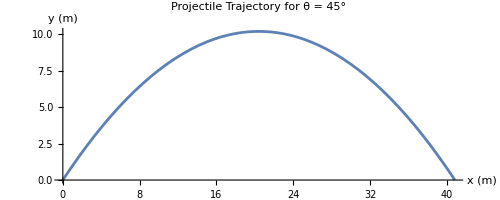

```mathematica
v0=20; (*Initial velocity in m/s*)
g=9.8; (*Acceleration due to gravity in m/s^2*)
θ=45 Degree; (*Launch angle in radians*)

(*Parametric equations for the projectile*)
x[t_]:=v0*Cos[θ]*t
y[t_]:=v0*Sin[θ]*t-(1/2)*g*t^2

(*Time of flight*)
tflight=(2*v0*Sin[θ])/g;

(*Parametric plot of the trajectory*)
ParametricPlot[{x[t],y[t]},{t,0,tflight},PlotRange->{{0,v0^2*Sin[2 θ]/g},{0,v0^2*Sin[θ]^2/(2 g)}},AxesLabel->{"x (m)","y (m)"},PlotLabel->"Projectile Trajectory for θ = 45°"]
```

Answer 4(iii)

```mathematica
Manipulate[ParametricPlot[{10 √2 Cos[θ] t ,10 √2 Cos[θ] t - 4.9 t^2},{t,0,10},PlotRange->{{0,45},{0,15}},AxesOrigin->{0,0},AxesLabel->{"x (m)","y (m)"},PlotLabel->{"Projectile Trajectory for θ = ",θ}],{θ, 0, Pi/2}]
```

Answer 4(iv)

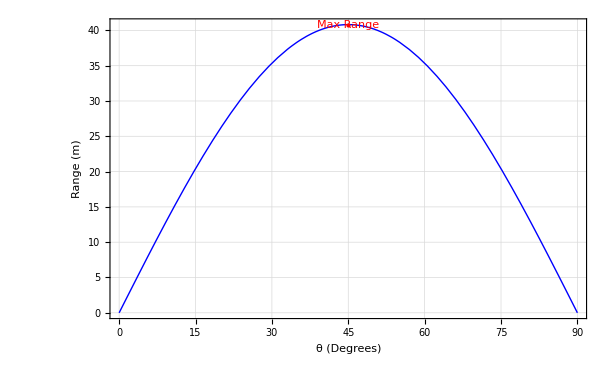

```mathematica
v0=20; (*Initial velocity*)
g=9.8; (*Acceleration due to gravity*)

range[θ_]:=(v0^2*Sin[2 θ])/g

Plot[range[θ Degree],{θ,0,90},AxesLabel->{"θ (Degrees)","Range (m)"},PlotStyle->{Thick,Blue},GridLines->Automatic,Epilog->{(*Mark the max range point*){Red,PointSize[Large],Point[{45,range[45 Degree]}]},Text[Style["Max Range",Red],{45,range[45 Degree]},{0,-2}]},Frame->True]
```

```mathematica
maxRangeAngle=Solve[D[range[θ],θ]==0,θ];
maxRangeAngleDegree=(θ/. maxRangeAngle)*180/Pi//N
```

{-45.,45.}

Answer 4(v)

```mathematica
Manipulate[ParametricPlot[{{10 √2 Cos[θ] t ,10 √2 Cos[θ] t - 4.9 t^2},{t,Tan[0.5°] t}},{t,0,45},PlotRange->{{0,45},{0,15}},AxesOrigin->{0,0}],{θ, 0, Pi/2}]
```

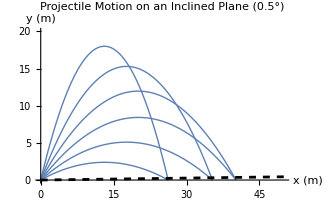

```mathematica
(*Define parameters*)g=9.81; (*Gravity in m/s^2*)
thetaGround=0.5 Degree; (*Ground inclination in degrees*)
v0=20; (*Initial velocity in m/s*)

(*Function for projectile motion*)
ProjectilePath[θ_]:=Module[{t,x,y},tmax=Solve[v0 Sin[θ] t-(1/2) g t^2==0,t][[2,1,2]];(*Flight time*){x,y}={v0 Cos[θ] t,v0 Sin[θ] t-(1/2) g t^2};
ParametricPlot[{v0 Cos[θ] t,v0 Sin[θ] t-(1/2) g t^2},{t,0,tmax},PlotRange->{{0,50},{0,20}},PlotStyle->Thick]];

(*Define inclined ground*)
InclinedGround=Plot[Tan[thetaGround] x,{x,0,50},PlotStyle->{Dashed,Black}];

(*Plot trajectories for different launch angles*)
angles={20,30,40,50,60,70}; (*Angles in degrees*)
trajectories=Table[ProjectilePath[θ Degree],{θ,angles}];

(*Show final plot*)
Show[trajectories,InclinedGround,AxesLabel->{"x (m)","y (m)"},PlotLabel->"Projectile Motion on an Inclined Plane (0.5°)",PlotLegends->Placed[LineLegend[angles,LegendLabel->"Angle (°)"],{0.8,0.7}]]
```

```mathematica
Clear[v0,θ,α,tf,R] 
(*Acceleration due to gravity in m/s^2 is predefined in mathematica*)
α=0.5 Degree; (*Convert degrees to radians*)

(*Step 2:Time of flight*)
tf=(2 v0 (Sin[θ]-Cos[θ] Tan[α]))/g;

(*Step 3:Range*)
R=(2 v0^2 Cos[θ] (Sin[θ]-Cos[θ] Tan[α]))/(g Cos[α]^2);

(*Step 4:Differentiate R with respect to θ and solve for θ*)
thetaOpt=Solve[D[R,θ]==0&&0<θ<Pi/2,θ];

(*Step 5:Extract numerical solutions and convert to degrees*)
thetaOptDegrees=θ/. thetaOpt//N;
thetaanswer=thetaOptDegrees*(180/Pi)
```

{45.25}

Answer 7

```mathematica
V=(a x^4)/4-(b x^2)/2
```

-(b x^2)/2+(a x^4)/4

```mathematica
F=-D[V,x](*If you run this before the previous cell, it'll give 0[obvio]*)
```

b x-a x^3

## (a)

```mathematica
Sol=Solve[F==0,x](*We have three equilibrium points*)
```

{{x→0},{x→-√(b/a)},{x→√(b/a)}}

## (b)

```mathematica
$Assumptions={a>0,b>0};(*Global assumption*)
DD=D[V,{x,2}];
Print["
Second derivative of potential energy is: ",DD]
For[i = 1,(*Start*)
	i<= 3, (*Test*)
	i++, (*Increment*)
(*Body*)
xvalue= Sol[[i]];
DDvalue=DD/.xvalue;
If[Simplify[DDvalue>0],
Print[Sol[[i]]," is an Unstable equilibrium point."],
Print[Sol[[i]]," is a Stable equilibrium point."]
]
]
```

Second derivative of potential energy is: -b+3 a x^2

{x→0} is a Stable equilibrium point.

{x→-√(b/a)} is an Unstable equilibrium point.

{x→√(b/a)} is an Unstable equilibrium point.